```mathematica
colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]};
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large];
alpha=20.4*π/180;
beta=68.7*π/180;
deltaAB=alpha-beta;
delta=94.54*π/180 (*Munir's reported 1.66 plus or minus .01*);

alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
rev=1;

Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
(* If given a list of files*)
GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
association=Append[association,rawFile[[k]][[1]]->StringJoin[ToString[DeleteCases[Take[rawFile[[k]],{2,-1}],Null]]]];
,
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];

StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 4 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 4 beta0]stokes[[1]]);
stokes];

StokesParametersFromRawFourierData[intensityArray_,rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
StokesParametersFromFourierCoefficients[fc,rev,alpha,beta0,delta]
];

StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_,rev_]:=
Module[{intensityArray,f},
intensityArray=Normal[polFile[[2]][All,"COUNT"]];
StokesParametersFromRawFourierData[intensityArray,rev,alpha,beta0,delta]
];

StokesParametersFromPolFileName[polFileName_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["#REV:"];
StokesParametersFromPolFile[f,alpha,beta0,delta,rev_]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];

AverageGetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetAverageCountRateFromFileNames[fileNames_]:=Module[{files},
files=ImportFile[fileNames];
GetAverageCountRateFromFiles[files]
];

(* See Nate Clayburn's explanation on Background Subtraction p. 129 eq. 93*)
(* Returns a list of two items.
	the first item is a list of the intensity reaching the PMT at each step of the polarimeter.
	the second item is the standard deviation of these counts
*)
GetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];


GetCurrentNormalizedAverageCountRateFromFiles[files_]:=Module[{t,scale,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,rev},
nDataPts=files[[1]][[1]]["#DATAPPR:"];
rev=files[[1]][[1]]["#REV:"];
(* This hasn't yet been implemented in the data collection files. As soon as it is, you can uncomment it.
scale=files[[1]][[1]]["#SCALE:"];*)
scale=6;
darkCountsRate=10;
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files]*rev;
t=dwell*nCycles;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/t/Abs[current[[j]]*10^(-scale)/(1*^-9)];
errorSum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/(t^2*(current[[j]]*10^(-scale)/(1*^-9))^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFileNames[fileNames_]:=Module[{filesPass,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
filesPass=ImportFile[fileNames];
GetCurrentNormalizedAverageCountRateFromFiles[filesPass]
];

AverageBackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
Print[darkCountsRate];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
rev=files[[i]][[1]]["#REV:"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageGetAverageCountRateFromFiles[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];
SignalRateCurrentNormFromRates::usage ="SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background."
SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["#DWELL(s):"];
nCycles=file[[1]]["#REV:"];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]/(nCycles*dwell)-(darkCountsRate[[1]][[j]])/nCycles)/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-(darkCountsRate[[2]][[j]])^2/(nCycles^2*current[[j]]^2)-(molyCountsRate[[2]][[j]])^2/(nCycles^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["#REV:"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

AverageStokes[stokesVectors_]:=Module[{i,transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes;
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=Mean[transposedValues[[i]]];
stokesStdDev[[i]]=StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
{stokes,stokesStdDev}
];

CalculateAverageStokesFromFilesAndCountRates[polFileNames_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes={0,0,0,0,0,0};
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];
Export["stokesValues.tsv",{polFileNames,stokesValues}];
AverageStokes[stokesValues]
]

NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];


GetIntensityArrayFromFileName[fileName_]:=Module[{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,{"ANGLE","COUNT"}]]
];

PlotRawPolFromFileName[fileName_]:=Module[
{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
ListPlot[intensityArray]
];
SetAttributes[PlotRawPolFromFileName,Listable];

PlotListOfPolFileNames[fileNames_,plotRange_:{Automatic,Automatic}]:=Module[{intensityArrays,i},
intensityArrays={};
For[i=1,i≤Length[fileNames],i++,
AppendTo[intensityArrays,Legended[GetIntensityArrayFromFileName[fileNames[[i]]],fileNames[[i]]]];
];
ListPlot[intensityArrays,PlotRange->plotRange]
];

GetStokesFromFileNames[fileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{i,stokes,signal,stokesData},
stokesData={};
signal=ImportFile[fileNames];
For[i=1,i≤Length[fileNames],i++,
stokes=StokesParametersFromPolFile[signal[[i]],alpha,beta,delta,signal[[i]][[1]]["#REV:"]];
AppendTo[stokesData,stokes];
];
stokesData
];
GetAverageFourierCoefficientsFromFileNames[fileNames]:=Module[{fc},
fc=GetFourierCoefficientsFromFileNames[fileNames]];

GetFourierCoefficientsFromFileNames[fileNames_]:=Module[{files,i,coefficientsList,intensityArray,revs},
files=ImportFile[fileNames];
coefficientsList={};
For[i=1,i≤Length[files],i++,
revs=files[[i]][[1]]["#REV:"];
intensityArray=Normal[files[[i]][[2]][All,"COUNT"]];
AppendTo[coefficientsList,DFT[intensityArray,revs]];
];
coefficientsList
];

GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames_,timeStamp_]:=Module[{exFileIndex,exFile,x},
exFileIndex=GetIndexOfFilenameFromTimestamp[excitationFileNames,timeStamp];
exFile=ImportFile[excitationFileNames[[exFileIndex]]];
aoutToElectronEnergyData=Normal[exFile[[2]][All,{"Aout","SecondaryElectronEnergy"}][[All,Values]]];
LinearModelFit[aoutToElectronEnergyData,x,x]
];
```

SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background.

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dropBoxfolderLaptop=FileNameJoin[{"/","home","karl","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,dataDump,pumpQWP,test.png,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-01-20_electronPolarization","data"}]];
polFileNames=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]]
excitationFileNames=FileNames[StringExpression["EX",__,"_",__,DigitCharacter,".dat"]]
```

{POL2018-01-20_194609.dat,POL2018-01-20_222343.dat,POL2018-01-20_222454.dat,POL2018-01-20_222607.dat,POL2018-01-20_222721.dat,POL2018-01-20_222834.dat,POL2018-01-20_222947.dat,POL2018-01-20_223101.dat,POL2018-01-20_223214.dat,POL2018-01-20_223327.dat,POL2018-01-20_223441.dat,POL2018-01-20_223553.dat,POL2018-01-20_223706.dat,POL2018-01-20_223952.dat,POL2018-01-20_224104.dat,POL2018-01-20_224218.dat,POL2018-01-20_224332.dat,POL2018-01-20_224444.dat,POL2018-01-20_224557.dat,POL2018-01-20_224711.dat,POL2018-01-20_224823.dat,POL2018-01-20_224937.dat,POL2018-01-20_225051.dat,POL2018-01-20_225203.dat,POL2018-01-20_225316.dat,POL2018-01-20_225602.dat,POL2018-01-20_225714.dat,POL2018-01-20_225827.dat,POL2018-01-20_225941.dat,POL2018-01-20_230054.dat,POL2018-01-20_230207.dat,POL2018-01-20_230321.dat,POL2018-01-20_230434.dat,POL2018-01-20_230547.dat,POL2018-01-20_230702.dat,POL2018-01-20_230814.dat,POL2018-01-20_230927.dat,POL2018-01-20_231213.dat,POL2018-01-20_231325.dat,POL2018-01-20_231438.dat,POL2018-01-20_231553.dat,POL2018-01-20_231705.dat,POL2018-01-20_231818.dat,POL2018-01-20_231932.dat,POL2018-01-20_232044.dat,POL2018-01-20_232158.dat,POL2018-01-20_232312.dat,POL2018-01-20_232424.dat,POL2018-01-20_232537.dat,POL2018-01-20_232823.dat,POL2018-01-20_232935.dat,POL2018-01-20_233048.dat,POL2018-01-20_233203.dat,POL2018-01-20_233316.dat,POL2018-01-20_233430.dat,POL2018-01-20_233543.dat,POL2018-01-20_233656.dat,POL2018-01-20_233809.dat,POL2018-01-20_233923.dat,POL2018-01-20_234035.dat,POL2018-01-20_234148.dat,POL2018-01-20_234434.dat,POL2018-01-20_234546.dat,POL2018-01-20_234700.dat,POL2018-01-20_234814.dat,POL2018-01-20_234926.dat,POL2018-01-20_235039.dat,POL2018-01-20_235153.dat,POL2018-01-20_235306.dat,POL2018-01-20_235419.dat,POL2018-01-20_235533.dat,POL2018-01-20_235645.dat,POL2018-01-20_235758.dat,POL2018-01-21_013049.dat,POL2018-01-21_013304.dat,POL2018-01-21_013521.dat,POL2018-01-21_013738.dat,POL2018-01-21_013954.dat,POL2018-01-21_014211.dat,POL2018-01-21_014428.dat,POL2018-01-21_014644.dat,POL2018-01-21_014900.dat,POL2018-01-21_015117.dat,POL2018-01-21_015333.dat,POL2018-01-21_015550.dat,POL2018-01-21_020156.dat,POL2018-01-21_020411.dat,POL2018-01-21_020628.dat,POL2018-01-21_020845.dat,POL2018-01-21_021101.dat,POL2018-01-21_021318.dat,POL2018-01-21_021536.dat,POL2018-01-21_021752.dat,POL2018-01-21_022008.dat,POL2018-01-21_022226.dat,POL2018-01-21_022442.dat,POL2018-01-21_022659.dat,POL2018-01-21_023305.dat,POL2018-01-21_023520.dat,POL2018-01-21_023737.dat,POL2018-01-21_023954.dat,POL2018-01-21_024210.dat,POL2018-01-21_024427.dat,POL2018-01-21_024644.dat,POL2018-01-21_024900.dat,POL2018-01-21_025116.dat,POL2018-01-21_025334.dat,POL2018-01-21_025550.dat,POL2018-01-21_025807.dat,POL2018-01-21_030413.dat,POL2018-01-21_030628.dat,POL2018-01-21_030845.dat,POL2018-01-21_031102.dat,POL2018-01-21_031318.dat,POL2018-01-21_031535.dat,POL2018-01-21_031752.dat,POL2018-01-21_032008.dat,POL2018-01-21_032224.dat,POL2018-01-21_032442.dat,POL2018-01-21_032657.dat,POL2018-01-21_032914.dat,POL2018-01-21_033520.dat,POL2018-01-21_033736.dat,POL2018-01-21_033952.dat,POL2018-01-21_034210.dat,POL2018-01-21_034425.dat,POL2018-01-21_034642.dat,POL2018-01-21_034859.dat,POL2018-01-21_035115.dat,POL2018-01-21_035331.dat,POL2018-01-21_035549.dat,POL2018-01-21_035805.dat,POL2018-01-21_040021.dat,POL2018-01-21_040627.dat,POL2018-01-21_040843.dat,POL2018-01-21_041059.dat,POL2018-01-21_041317.dat,POL2018-01-21_041533.dat,POL2018-01-21_041749.dat,POL2018-01-21_042006.dat,POL2018-01-21_042222.dat,POL2018-01-21_042439.dat,POL2018-01-21_042656.dat,POL2018-01-21_042912.dat,POL2018-01-21_043128.dat}

{EX2018-01-20_194206.dat,EX2018-01-20_221123.dat,EX2018-01-21_005105.dat,EX2018-01-21_010728.dat,EX2018-01-21_015806.dat,EX2018-01-21_022915.dat,EX2018-01-21_030023.dat,EX2018-01-21_033131.dat,EX2018-01-21_040238.dat,EX2018-01-21_043345.dat,EX2018-01-21_114835.dat}

```mathematica
fit=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,"221123"];
fit[516]
fit[324]
fit[36]
```

26.0358

31.976

40.8862

```mathematica
runs=6; (*The number of Electron Polarization Runs*)
aouts=Reverse[{36,324,516}]; (* A list of the AOUTs or energies at which we collected data*)
energies=aouts;
aoutToEnergy=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,"221123"];
For[i=1,i≤Length[aouts],i++,energies[[i]]=aoutToEnergy[aouts[[i]]]];
pumpLights={"noPump","piPump","s+Pump","s-Pump"};
startFile=GetIndexOfFilenameFromTimestamp[polFileNames,"222343"];

fileNames=<||>;
allFiles=<||>;

For[j=0,j<Length[pumpLights],j++,
For[i=startFile,i<Length[energies]+startFile,i++,
listONames=Take[polFileNames,{i+j*Length[energies],i+Length[energies]*runs*Length[pumpLights]-j-(i-startFile)-1,Length[energies]*Length[pumpLights]}];
AppendTo[fileNames,energies[[i-startFile+1]]->listONames];
];
AppendTo[allFiles,pumpLights[[j+1]]->fileNames];
];
allFiles;
energyPlots=<||>;
```

## Taking the average counts from all the runs and manipulating beta to minimize P_2

```mathematica
cr=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[1]][[3]],allFiles[[2]][[3]],allFiles[[3]][[3]],allFiles[[4]][[3]]]][[1]],1]
alpha=20.4;
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[cr,1,alpha*π/180,beta*π/180,delta],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.03,.03}}],{beta,0.001,90,.1}]
```

{{{0.,22.6915,68.2777,4.29467,-43.6175,7.05223,4.75208,6.41244,0.94882,0.86746,2.50947,1.85095,3.64401,2.66348,1.67278,4.50972,2.42793,0.426965,2.28385,-1.26346,0.574544,-1.80887,3.76517,-0.824943,-0.423998,0.0783227,4.60784,-3.52821,-1.08149,0.0247698},{}},{{2580.86,2.7681,38.0303,4.72035,37.3575,3.3766,1.11574,-2.70378,1.09588,0.803354,2.21088,1.01779,-1.91388,-1.56848,0.513826,2.68009,-1.89727,-1.26415,7.4875,-0.59642,1.49606,2.23706,-2.62471,3.4688,-0.387971,-0.603912,-0.276113,0.128592,4.17696,-1.60005},{}}}

Part::partw: Part 3 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 5 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 3 of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«10»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 5 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 3 of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«10»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
allFiles
```

<|noPump→<|26.0358→{POL2018-01-20_222343.dat,POL2018-01-20_223952.dat,POL2018-01-20_225602.dat,POL2018-01-20_231213.dat,POL2018-01-20_232823.dat,POL2018-01-20_234434.dat},31.976→{POL2018-01-20_222454.dat,POL2018-01-20_224104.dat,POL2018-01-20_225714.dat,POL2018-01-20_231325.dat,POL2018-01-20_232935.dat,POL2018-01-20_234546.dat},40.8862→{POL2018-01-20_222607.dat,POL2018-01-20_224218.dat,POL2018-01-20_225827.dat,POL2018-01-20_231438.dat,POL2018-01-20_233048.dat,POL2018-01-20_234700.dat}|>,piPump→<|26.0358→{POL2018-01-20_222721.dat,POL2018-01-20_224332.dat,POL2018-01-20_225941.dat,POL2018-01-20_231553.dat,POL2018-01-20_233203.dat,POL2018-01-20_234814.dat},31.976→{POL2018-01-20_222834.dat,POL2018-01-20_224444.dat,POL2018-01-20_230054.dat,POL2018-01-20_231705.dat,POL2018-01-20_233316.dat,POL2018-01-20_234926.dat},40.8862→{POL2018-01-20_222947.dat,POL2018-01-20_224557.dat,POL2018-01-20_230207.dat,POL2018-01-20_231818.dat,POL2018-01-20_233430.dat,POL2018-01-20_235039.dat}|>,s+Pump→<|26.0358→{POL2018-01-20_223101.dat,POL2018-01-20_224711.dat,POL2018-01-20_230321.dat,POL2018-01-20_231932.dat,POL2018-01-20_233543.dat,POL2018-01-20_235153.dat},31.976→{POL2018-01-20_223214.dat,POL2018-01-20_224823.dat,POL2018-01-20_230434.dat,POL2018-01-20_232044.dat,POL2018-01-20_233656.dat,POL2018-01-20_235306.dat},40.8862→{POL2018-01-20_223327.dat,POL2018-01-20_224937.dat,POL2018-01-20_230547.dat,POL2018-01-20_232158.dat,POL2018-01-20_233809.dat,POL2018-01-20_235419.dat}|>,s-Pump→<|26.0358→{POL2018-01-20_223441.dat,POL2018-01-20_225051.dat,POL2018-01-20_230702.dat,POL2018-01-20_232312.dat,POL2018-01-20_233923.dat},31.976→{POL2018-01-20_223553.dat,POL2018-01-20_225203.dat,POL2018-01-20_230814.dat,POL2018-01-20_232424.dat,POL2018-01-20_234035.dat},40.8862→{POL2018-01-20_223706.dat,POL2018-01-20_225316.dat,POL2018-01-20_230927.dat,POL2018-01-20_232537.dat,POL2018-01-20_234148.dat}|>|>

## This time, taking all of the no Pump runs and manipulating beta to minimize P3:C2 (5)

```mathematica
cr=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[1]][[2]],allFiles[[1]][[3]],allFiles[[2]][[2]],allFiles[[2]][[3]]]][[1]],1]
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[cr,1,alpha*π/180,beta*π/180,π/2],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{alpha,0.001,180,.1},{beta,0.001,90,.1}]
```

{{{0.,1.1784,2.62001,0.284943,-17.5553,1.18104,0.503914,0.85219,1.04702,0.738895,0.256199,-0.892243,1.91462,-0.0190515,-1.84368,0.202778,-2.32686,0.192369,-1.19313,0.387646,-1.38444,-1.56172,-1.41061,0.157624,-2.42745,-1.8741,0.565086,-1.77583,0.185493,-0.736445},{}},{{799.559,-1.25906,1.61471,0.651857,18.0906,0.25205,-0.268724,0.605558,1.04297,-0.902889,0.332639,1.91982,0.724006,-1.01814,0.134614,2.09861,-0.330684,1.00172,0.881919,1.65872,-0.771528,-2.33619,0.559578,-1.18869,0.210021,-1.46316,0.250819,1.95389,2.11104,0.200457},{}}}

Part::partd: Part specification cr⟦2⟧ is longer than depth of object.

Part::partd: Part specification cr⟦1⟧ is longer than depth of object.

Part::partd: Part specification cr⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 5 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 3 of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«10»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

## Now all S+ runs, maximize P3:C2

```mathematica
crPlus=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[3]][[2]],allFiles[[3]][[3]]]][[1]],1]
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[crPlus,1,alpha*π/180,beta*π/180,π/2],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{alpha,0.01,180,.5},{beta,0.01,90,.5}]
```

{{{0.,0.112013,7.86545,0.182234,-17.4846,0.619392,0.172602,0.35258,1.47301,-1.3259,-1.2413,1.23422,-1.06929,0.584217,2.18588,1.15556,1.67486,-1.04522,-0.281918,0.84018,-3.02628,-0.864216,-0.674595,-0.30395,-0.467361,-2.27217,-1.82751,-2.27791,3.32295,-0.708431},{}},{{791.401,-1.22299,4.55841,-1.07074,16.5541,-2.43635,0.854202,-1.64415,2.00489,1.58666,-0.905556,1.67095,2.14285,-0.839731,-1.39715,0.463889,-0.280488,0.292928,-0.527813,0.0968666,-0.697222,-1.56031,-0.105023,-2.84351,-1.65535,-1.3442,-1.6993,-0.586167,3.9673,-0.239907},{}}}

Part::partd: Part specification crPlus⟦2⟧ is longer than depth of object.

Part::partd: Part specification crPlus⟦1⟧ is longer than depth of object.

Part::partd: Part specification crPlus⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

## Now all S- runs, maximize P3:C2

```mathematica
crMinus=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[4]][[2]],allFiles[[4]][[3]]]][[1]],1]
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[crMinus,1,alpha*π/180,beta*π/180,π/2],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{alpha,0.01,180,.5},{beta,0.01,90,.5}]
```

{{{0.,1.78115,-0.303387,-1.83037,-17.3361,0.163115,1.52605,-0.171453,-0.368338,-1.02368,-1.23842,-0.846395,-3.96541,-2.08349,1.10373,2.17667,-0.707989,0.0903758,0.314222,-0.720683,1.93701,-2.06505,1.00703,1.5837,1.10669,-1.32645,2.50454,0.364977,-0.493443,0.510236},{}},{{794.387,-2.24751,-0.33663,3.08742,17.7552,-0.386699,-2.20388,-1.68475,-2.0385,0.377871,-0.488333,1.05104,3.92549,0.642063,1.66628,0.37,0.513277,1.20567,0.095545,-1.14813,1.38833,0.031484,-0.972415,-2.52234,-2.00382,-0.473301,0.00609991,-2.35011,2.02337,-1.57636},{}}}

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦1⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦1⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
colorBlindPallete
```

{RGBColor[Rational[46, 51], Rational[53, 85], 0],RGBColor[Rational[86, 255], Rational[12, 17], Rational[233, 255]],RGBColor[0, Rational[158, 255], Rational[23, 51]],RGBColor[Rational[16, 17], Rational[76, 85], Rational[22, 85]],RGBColor[0, Rational[38, 85], Rational[178, 255]],RGBColor[Rational[71, 85], Rational[94, 255], 0],RGBColor[Rational[4, 5], Rational[121, 255], Rational[167, 255]],RGBColor[0, 0, 0]}

```mathematica
Rasterize[energyPlots[[2]],ImageResolution->200]
```

-Graphics-

## Display all raw data and averages

Pump Light: noPump, Energy: 22.63

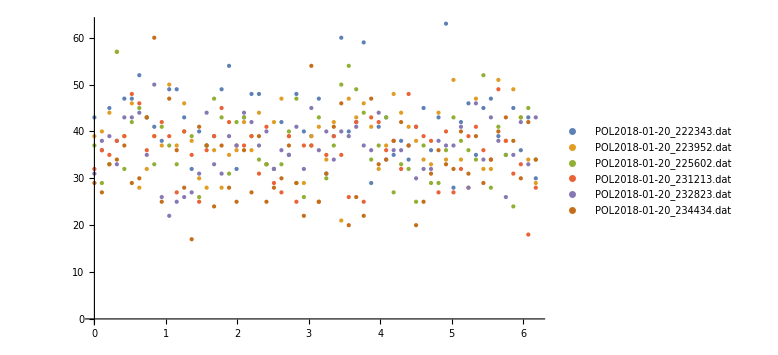

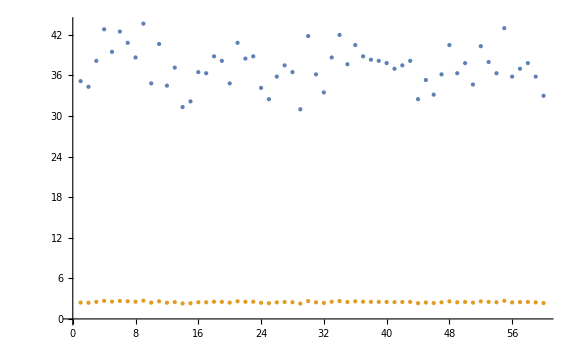

Pump Light: noPump, Energy: 27.49

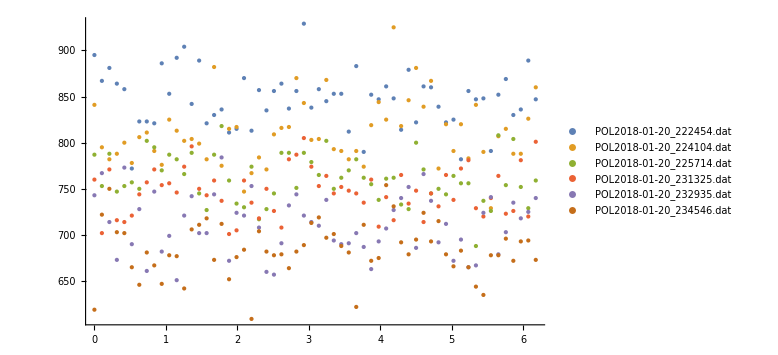

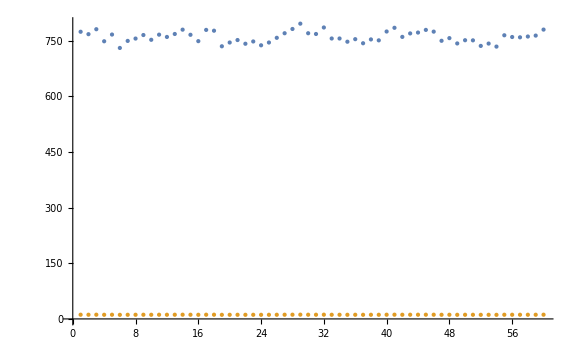

Pump Light: noPump, Energy: 36.55

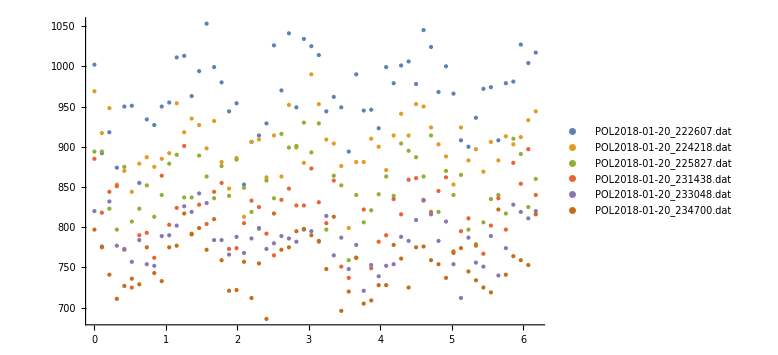

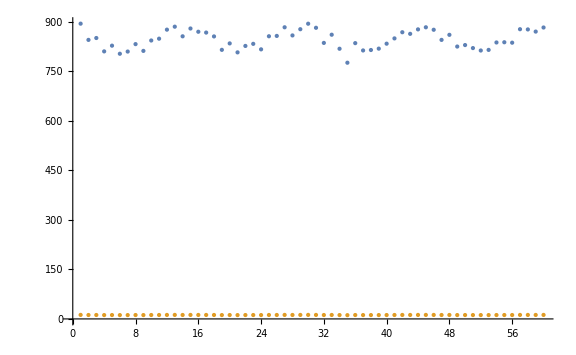

Pump Light: piPump, Energy: 22.63

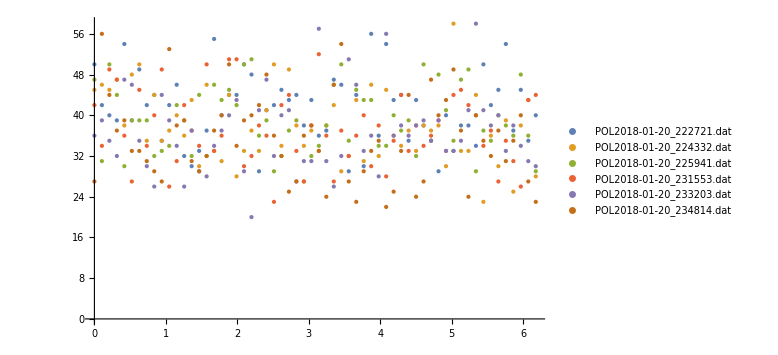

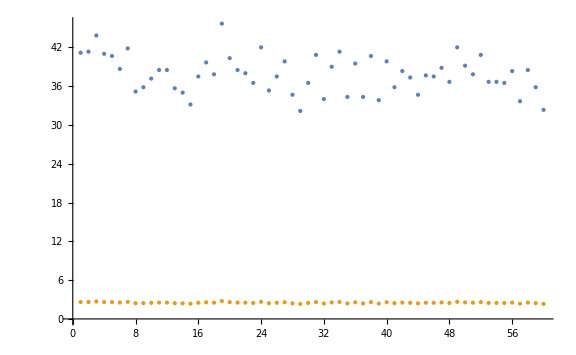

Pump Light: piPump, Energy: 27.49

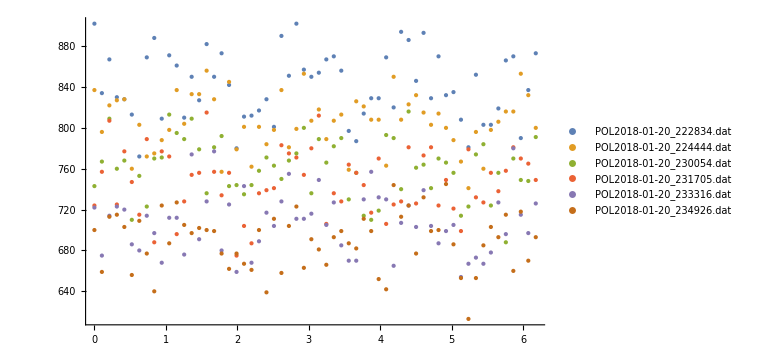

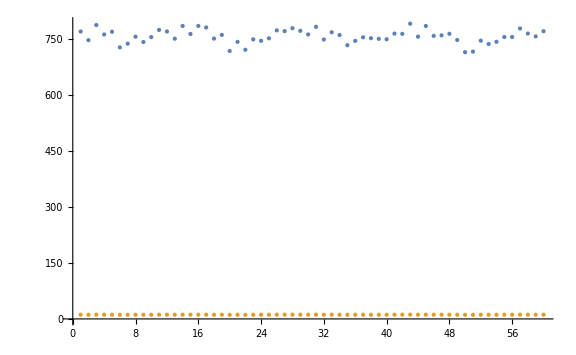

Pump Light: piPump, Energy: 36.55

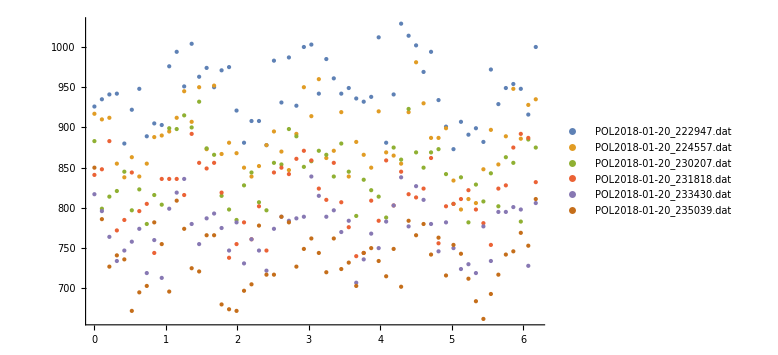

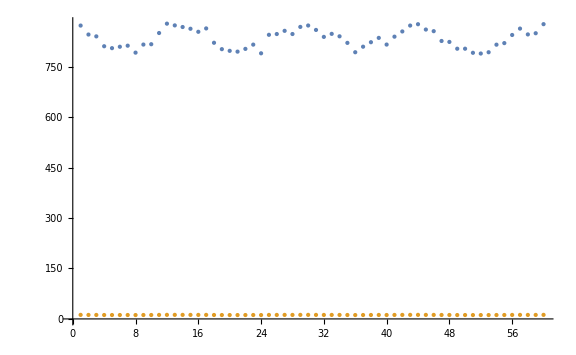

Pump Light: s+Pump, Energy: 22.63

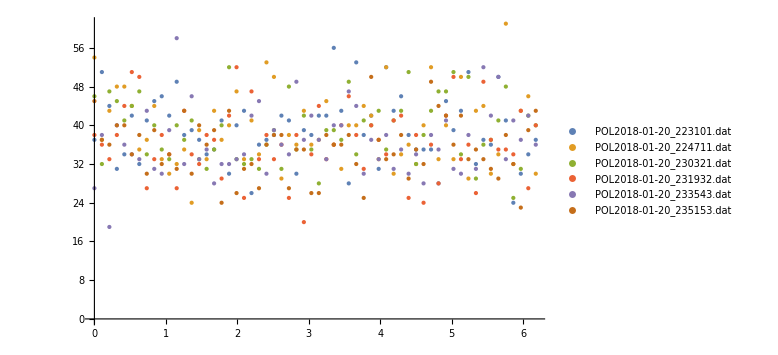

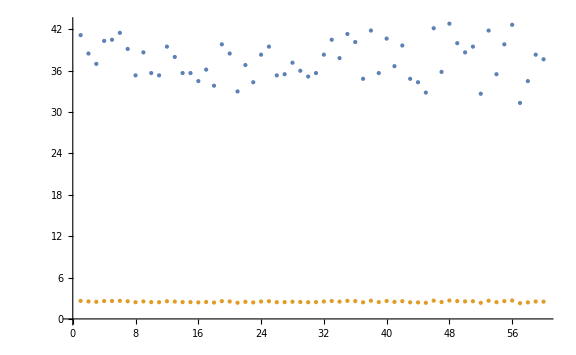

Pump Light: s+Pump, Energy: 27.49

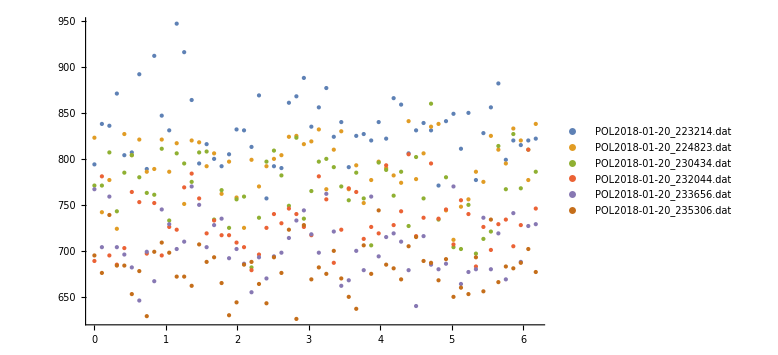

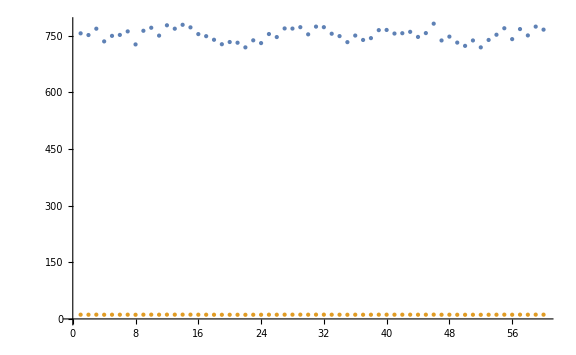

Pump Light: s+Pump, Energy: 36.55

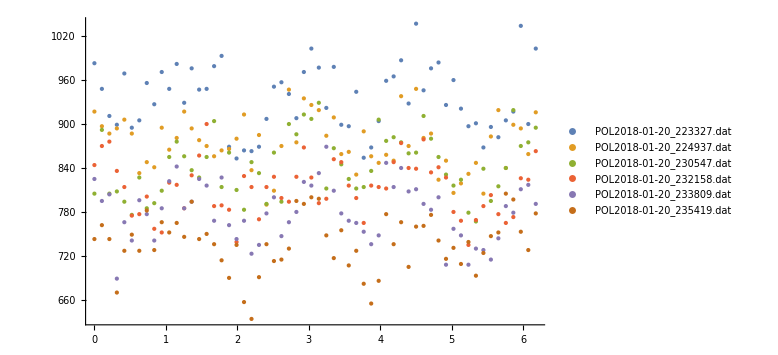

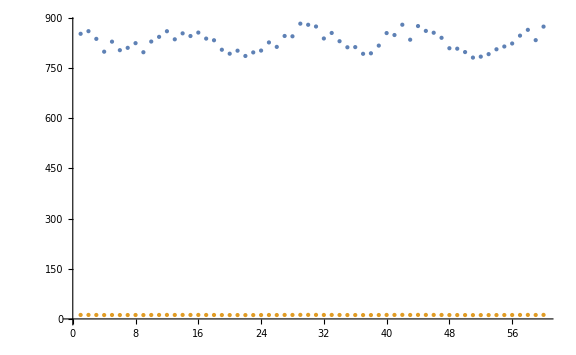

Pump Light: s-Pump, Energy: 22.63

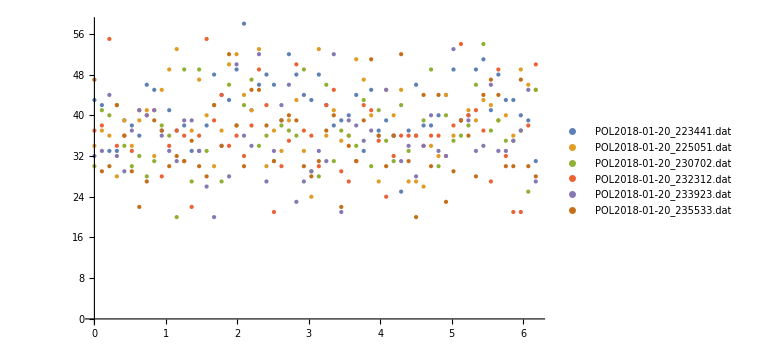

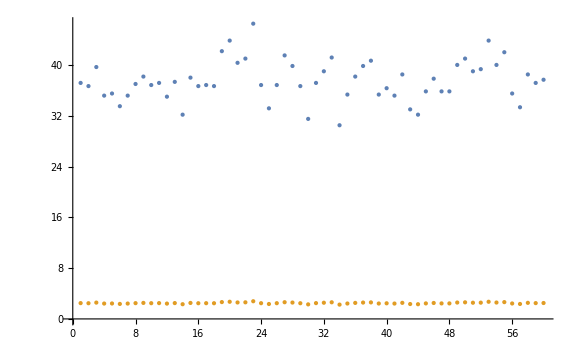

Pump Light: s-Pump, Energy: 27.49

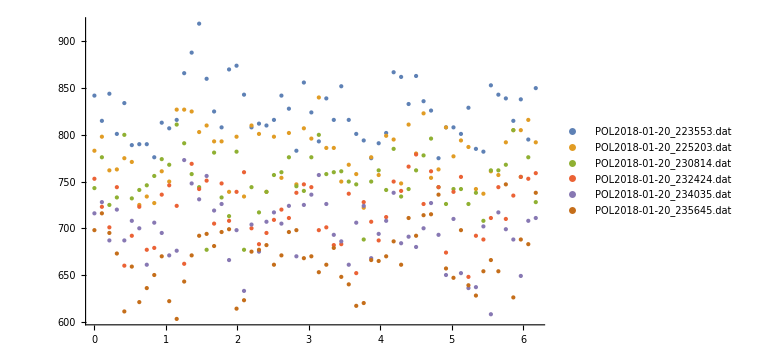

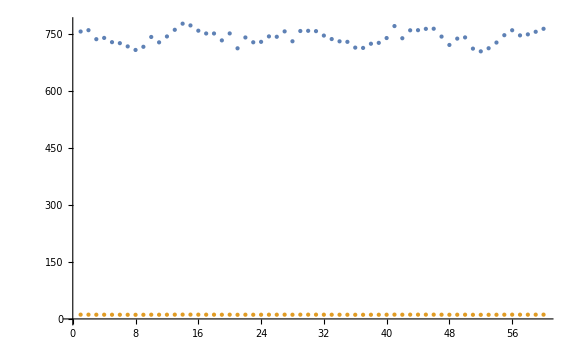

Pump Light: s-Pump, Energy: 36.55

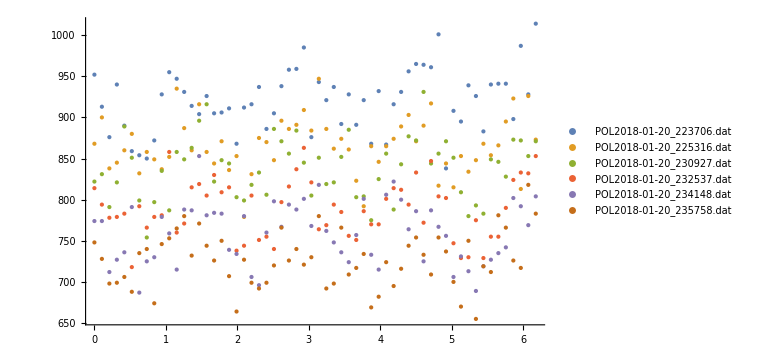

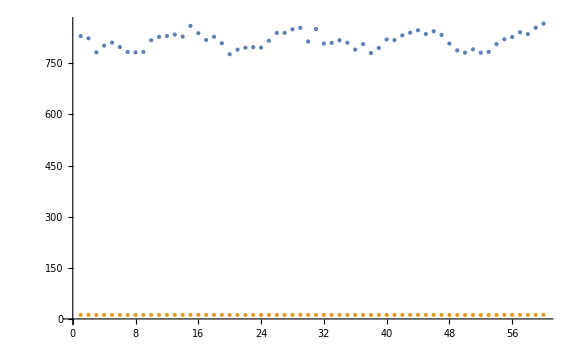

```mathematica
allStokes=<||>;
stokes=<||>;
For[j=1,j<=Length[allFiles],j++,
For[i=1,i<=Length[allFiles[[j]]],i++,
Print["Pump Light: "<>ToString[Keys[allFiles][[j]]]<>", Energy: "<>ToString[Keys[allFiles[[j]]][[i]]]]; 
Print[PlotListOfPolFileNames[allFiles[[j]][[i]]]];
Print[ListPlot[GetAverageCountRateFromFileNames[allFiles[[j]][[i]]]]];
AppendTo[stokes,Keys[allFiles[[j]]][[i]]->GetStokesFromFileNames[allFiles[[j]][[i]]]]
];
AppendTo[allStokes,Keys[allFiles][[j]]->stokes]
];
```

```mathematica
GetIndexOfFilenameFromTimestamp[polFileNames,"223327"]
```

10

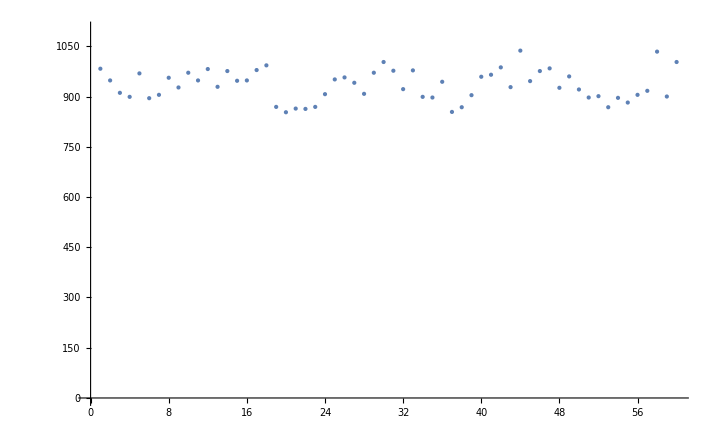

```mathematica
ListPlot[Normal[ImportFile[polFileNames[[10]]][[2]][All,"COUNT"]],PlotRange->{Automatic,{0,1100}}]
```

```mathematica
noPumpLowEng=allFiles["s-Pump"][[1]];
ImportFile[noPumpLowEng[[1]]]
stokes=GetStokesFromFileNames[noPumpLowEng];
ListPlot[Transpose[stokes],PlotLabel-> "Polarization Values Over Time",PlotRange->{-.1,.1},AxesLabel->{"Run Number","Percent Polarization"} ,PlotLegends->{"P_0","P_1","P_2","|P_3|","P_(3  C2)","P_(3  S2)"}];
PlotRawPolFromFileName[noPumpLowEng];
GetFourierCoefficientsFromFileNames[noPumpLowEng];
```

{<|#File→/home/pi/RbData/2018-01-20/POL2018-01-20_223441.dat,#Comments→Run,#IonGauge(Torr):→0.000176,#CVGauge(N2)(Torr):→1.05,#CVGauge(He)(Torr):→0.000984,#CURTEMP_R(degC):→140.,#SETTEMP_R(degC):→140.,#CURTEMP_T(degC):→199.9,#SETTEMP_T(degC):→200.,#AOUT:→516,#LEAKCURR:→0.0002,#AOUTCONV:→0.030938,#REV:→1,#DATAPPR:→60,#STPPERREV:→1200,#DATPTS:→60,#DWELL(s):→1|>,Dataset[<>]}

{<|#File→/home/pi/RbData/2018-01-20/POL2018-01-20_223706.dat,#Comments→Run,#IonGauge(Torr):→0.000176,#CVGauge(N2)(Torr):→1.05,#CVGauge(He)(Torr):→0.000995,#CURTEMP_R(degC):→140.,#SETTEMP_R(degC):→140.,#CURTEMP_T(degC):→199.9,#SETTEMP_T(degC):→199.9,#AOUT:→36,#LEAKCURR:→0.0002,#AOUTCONV:→0.030938,#REV:→1,#DATAPPR:→60,#STPPERREV:→1200,#DATPTS:→60,#DWELL(s):→1|>,Dataset[<>]}

74

145

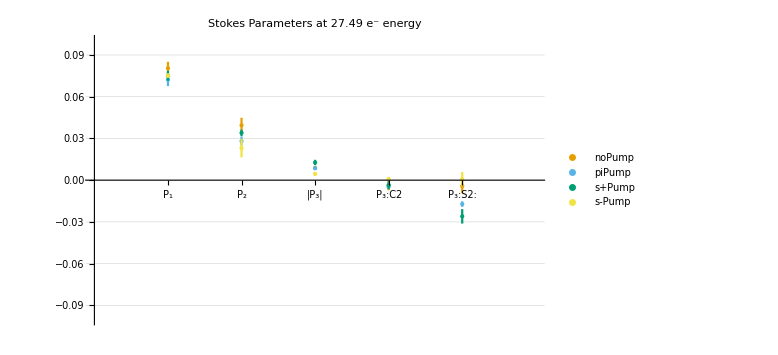
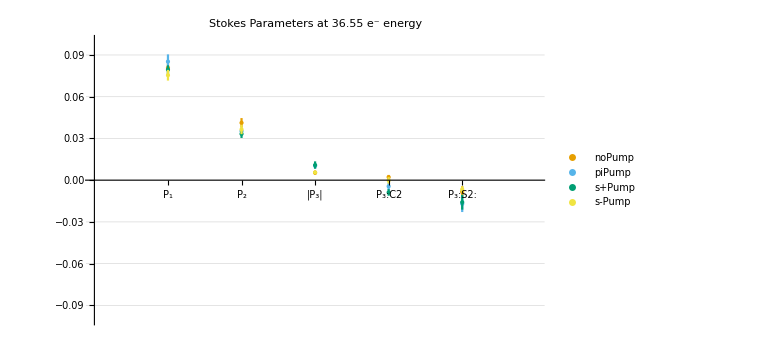
<|27.49→-Graphics-,36.55→-Graphics-|>

```mathematica
runs=6; (*The number of Electron Polarization Runs*)
energies={22.63,27.49,36.55}; (* A list of the AOUTs or energies at which we collected data*)
pumpLights={"noPump","piPump","s+Pump","s-Pump"};
excitationFile=GetIndexOfFilenameFromTimestamp[polFileNames,
startFile=GetIndexOfFilenameFromTimestamp[polFileNames,"013049"]
Length[polFileNames]
fileNames=<||>;
allFiles=<||>;

For[j=0,j<Length[pumpLights],j++,
For[i=startFile,i<Length[energies]+startFile,i++,
listONames=Take[polFileNames,{i+j*Length[energies],i+Length[energies]*runs*Length[pumpLights]-j-(i-startFile)-1,Length[energies]*Length[pumpLights]}];
AppendTo[fileNames,energies[[i-startFile+1]]->listONames];
];
AppendTo[allFiles,pumpLights[[j+1]]->fileNames];
];
allFiles;
energyPlots=<||>;

For[m=2,m≤Length[allFiles[[1]]],m++,
energyIndex=m;
darkCounts={ConstantArray[10,60],ConstantArray[3.3,60]};
stokes=<||>;
For[i=1,i≤Length[Keys[allFiles]],i++,
molyCounts=GetCurrentNormalizedAverageCountRateFromFileNames[allFiles[[i]][[1]]];
AppendTo[stokes,Keys[allFiles][[i]]->CalculateAverageStokesFromFilesAndCountRates[allFiles[[i]][[energyIndex]],molyCounts,darkCounts]];
];

plots={};

For[i=1,i≤Length[stokes],i++,
s=stokes[[i]];
plotData={};
For[k=2,k≤Length[s[[1]]],k++,
AppendTo[plotData,{{k-1,s[[1]][[k]]},ErrorBar[s[[2]][[k]]]}];
];
AppendTo[plots,ErrorListPlot[Legended[plotData,Keys[stokes][[i]]],GridLines->Automatic,ImageSize->{960,600},PlotRange->{{0,6},{-.1,.1}},PlotStyle->colorBlindPallete[[i]],Ticks->{{{1,"P_1"},{2,"P_2"},{3,"|P_3|"},{4,"P_3:C2"},{5,"P_3:S2:"}},Automatic}]];
];
AppendTo[energyPlots,Keys[allFiles[[1]]][[m]]->Show[plots,ImageSize->Large,PlotLabel->"Stokes Parameters at "<>ToString[Keys[allFiles[[1]]][[energyIndex]]]<>" e^- energy"]];
];
energyPlots
```

```mathematica
Rasterize[Show[energyPlots[[1]]],ImageResolution-> 200]
```

-Graphics-